# Ejercicios 1

## Programa

#### plantilla programa

```mathematica
(*programa para máximos y mínimos*) 
maxminint[f_,a_,b_]:=Module[{},
(*funcion primera derivasa*)
d1=D[f,x];
(*Sistema de ecuaciones del resultado de la derivada*)
sol=NSolve[D[f,x]==0 && a<x<b,x];
(*segunda derivada*)
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

## 13

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #13*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
```

```mathematica
f=(2 x^2)/(x-2);
```

Maximo en =  0.

Minimo en x = 4.

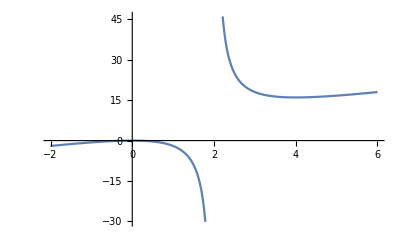

```mathematica
maxminint[f,-∞,∞]
```

## 14

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #14*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f= 1-x-(x^2-1);
```

Maximo en =  -0.5

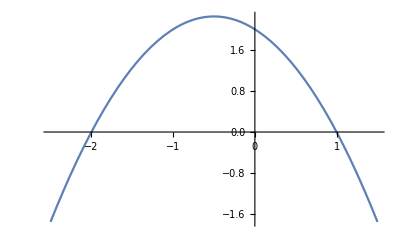

```mathematica
maxminint[f,-∞,∞]
```

```mathematica
f/.sol (*distancia máxima entre las 2 distancias*)
```

{2.25}

## 15

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #15*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f= 100(1+Cos[x])Sin[x];
```

Maximo en =  1.0472

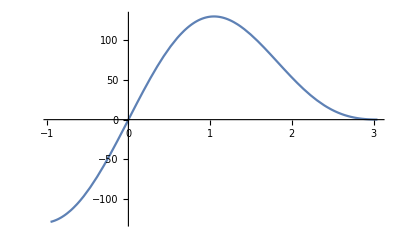

```mathematica
maxminint[f,0, π/2]
```

```mathematica
(x/.sol)  180/π
```

{60.}

## Longitud de arco

```mathematica
(*programa para realizar longitud de arco con una integral definida*)
(**)
longarc[f_,a_,b_]:=Module[{},
N[∫_a^b √(1+(D[f,x])^2)ⅆx]

]
```

```mathematica
f=x^2;
```

```mathematica
longarc[f,-1,3]
```

11.226

```mathematica
(*programa para realizar longitud de arco con una integral definida*)
(*con listas*)
longarc[f_,a_]:=Module[{},
N[∫_a[[1]]^a[[2]] √(1+(D[f,x])^2)ⅆx]

]
```

```mathematica
f=x^2;
```

```mathematica
longarc[f,{-1,3}]
```

11.226

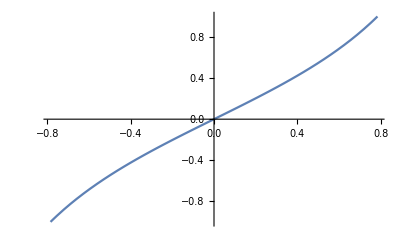

```mathematica
Plot[Tan[x],{x,-π/4,π/4}]
```

#### ejercicio 13 longitud de arco

```mathematica
(*programa para realizar longitud de arco con una integral definida*)
(*ejercicio 13*)
longarc[f_,a_,b_]:=Module[{},
N[∫_a^b √(1+(D[f,x])^2)ⅆx]

]
```

## Calculo de Áreas

#### Ejercicios 31-48

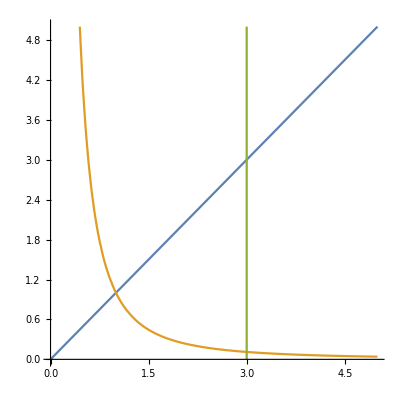

```mathematica
ContourPlot[{y==x,y==1/x^2,x==3},{x,0,5},{y,0,5},Frame->False,Axes->True]
```

```mathematica
NSolve[{y==x,y==1/x^2},{x,y},Reals](*Sistema de ecuaciones intersección de la ecuacion*)
```

{{x→1.,y→1.}}

```mathematica
NSolve[{y==1/x^2,x==3},{x,y},Reals]
```

{{x→3.,y→0.111111}}

```mathematica
NSolve[{y== x,x==3},{x,y},Reals]
```

{{x→3.,y→3.}}

```mathematica
N[∫_1^3 ∫_(1/x^2)^x 1ⅆyⅆx]
```

3.33333

#### ejercicio 32

```mathematica
N[∫_1^9 ∫_(1/x^2)^(x^2) 9ⅆyⅆx]
```

2176.

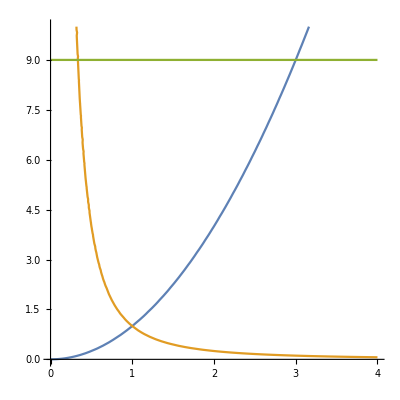

```mathematica
ContourPlot[{y==x^2,y==1/x^2,y==9},{x,0,4},{y,0,10},Frame->False,Axes->True]
```

```mathematica
NSolve[{y==x^2,y==1/x^2&& x≥0 },{x,y},Reals](*Sistema de ecuaciones intersección de la ecuacion*)
```

{{x→1.,y→1.}}

```mathematica
N[∫_1^9 ∫_(1/(√y))^(√y) 1ⅆxⅆy]
```

13.3333

#### ejercicio 43

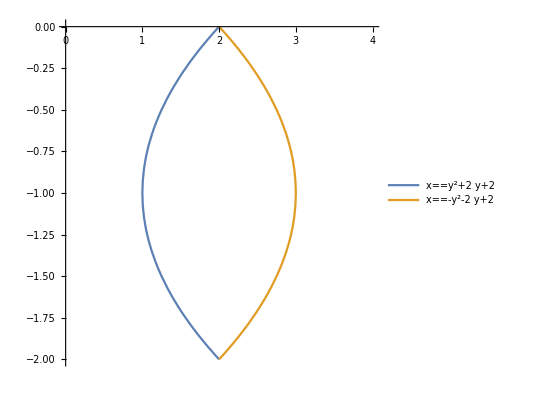

```mathematica
ContourPlot[{x==y^2+2y+2,x== -y^2-2y+2},{x,0,4},{y,-2,0},Frame->False,Axes->True,PlotLegends->"Expressions"]
(*con Plot legends mostramos que limite es el superior y el inferior línea amarilla es el límite superior de la primer integraldebido a que esta más adelante de la gráfica*)
```

```mathematica
NSolve[{x==y^2+2y+2,x== -y^2-2y+2},{x,y},Reals]
```

{{x→2.,y→-2.},{x→2.,y→0.}}

```mathematica
N[∫_-2^0 ∫_(y^2+2y+2)^(-y^2-2y+2) 1ⅆxⅆy,10]
```

2.666666667

#### ejercicio 44

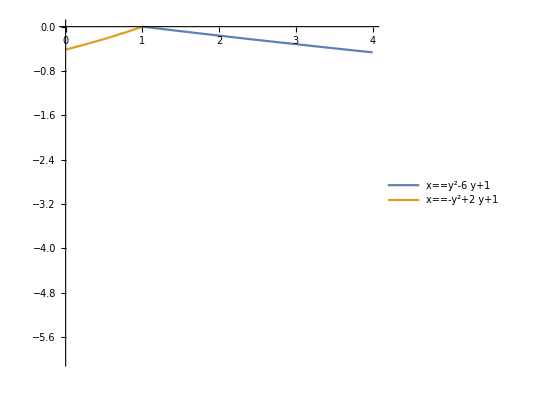

```mathematica
ContourPlot[{x==y^2-6y+1, x==-y^2+2y+1},{x,0,4},{y,-6,0},Frame->False,Axes->True,PlotLegends->"Expressions"]
(*con Plot legends mostramos que limite es el superior y el inferior línea amarilla es el límite superior de la primer integraldebido a que esta más adelante de la gráfica*)
```

```mathematica
NSolve[{x==y^2-6y+1,x== -y^2+2y+1},{x,y},Reals]
```

{{x→-7.,y→4.},{x→1.,y→0.}}

```mathematica
N[∫_-6^0 ∫_(y^2-6 y+1)^(-y^2-6 y+1) 1ⅆxⅆy,10]
```

NIntegrate::inumr: The integrand -2 y^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[-2 y^2,{y,-6,0},WorkingPrecision→20.,AccuracyGoal→∞,PrecisionGoal→10.]

## centro de masa

#### ejercicio 29

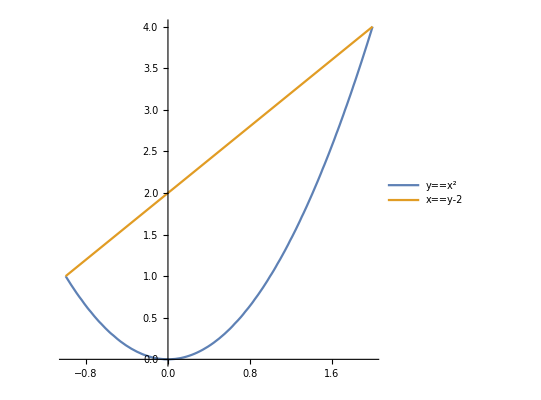

```mathematica
ContourPlot[{y==x^2, x==y-2},{x,-1,2},{y,0,4},Frame->False,Axes->True,PlotLegends->"Expressions"]
(*con Plot legends mostramos que limite es el superior y el inferior línea amarilla es el límite superior de la primer integraldebido a que esta más adelante de la gráfica*)
```

```mathematica
NSolve[{y==x^2, x==y-2},{x,y},Reals]
```

{{x→2.,y→4.},{x→-1.,y→1.}}

```mathematica
{N[∫_-1^2 ∫_(x^2)^(x+2) xⅆyⅆx,5]/N[∫_-1^2 ∫_(x^2)^(x+2) 1ⅆyⅆx,5],N[∫_-1^2 ∫_(x^2)^(x+2) yⅆyⅆx,5]/N[∫_-1^2 ∫_(x^2)^(x+2) 1ⅆyⅆx,5]}
```

{0.5,1.6}

```mathematica
Graphics[Point[{0.5,1.6}]]
```

-Graphics-

```mathematica
Graphics[{PointSize[Large],Point[{0.5,1.6}]}]
```

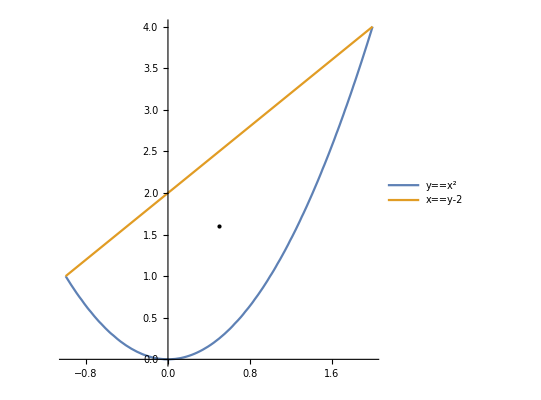

```mathematica
Show[ContourPlot[{y==x^2, x==y-2},{x,-1,2},{y,0,4},Frame->False,Axes->True,PlotLegends->"Expressions"],Graphics[{PointSize[Large],Point[{0.5,1.6}]}]]
```

#### ejercicio 30

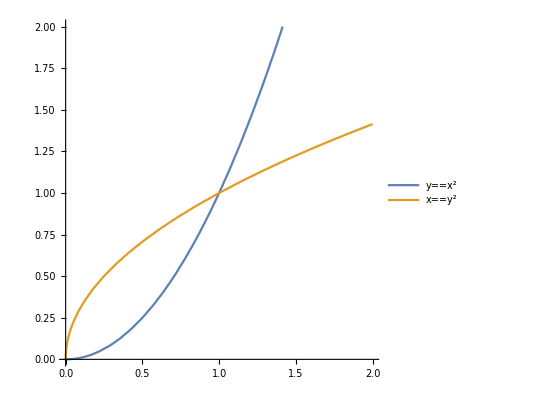

```mathematica
ContourPlot[{y==x^2, x==y^2},{x,0,2},{y,0,2},Frame->False,Axes->True,PlotLegends->"Expressions"]
```

```mathematica
NSolve[{y==x^2, x==y^2},{x,y},Reals]
```

{{x→1.,y→1.},{x→0.,y→0.}}

```mathematica
{N[∫_0^1 ∫_(x^2)^(√x) xⅆyⅆx,5]/N[∫_0^1 ∫_(x^2)^(√x) 1ⅆyⅆx,5],N[∫_0^1 ∫_(x^2)^(√x) yⅆyⅆx,5]/N[∫_0^1 ∫_(x^2)^(√x) 1ⅆyⅆx,5]}
```

{0.45,0.45}

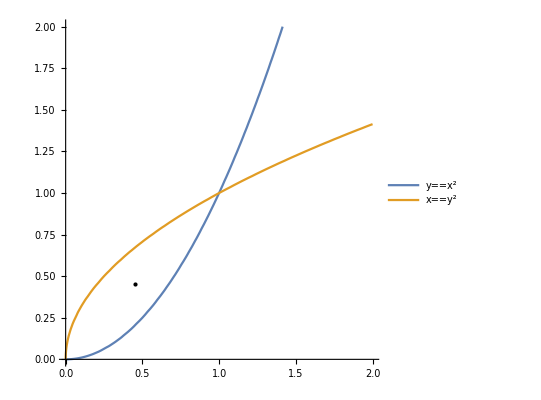

```mathematica
Show[ContourPlot[{y==x^2, x==y^2},{x,0,2},{y,0,2},Frame->False,Axes->True,PlotLegends->"Expressions"],Graphics[{PointSize[Large],Point[{0.45000,0.45000}]}]]
```

#### ejercicio 31

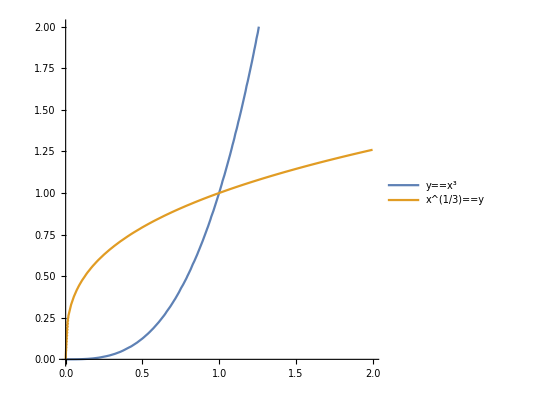

```mathematica
ContourPlot[{y==x^3, x^(1/3)==y},{x,0,2},{y,0,2},Frame->False,Axes->True,PlotLegends->"Expressions"]
```

```mathematica
NSolve[{y==x^3, x^(1/3)==y},{x,y},Reals]
```

{{x→1.,y→1.},{x→0,y→0},{x→0,y→0}}

```mathematica
Solve[x^(1/3)==y,y]
```

{{y→x^(1/3)}}

```mathematica
{N[∫_0^1 ∫_(x^3)^(x^(1/3)) xⅆyⅆx,5]/N[∫_0^1 ∫_(x^3)^(x^(1/3)) 1ⅆyⅆx,5],N[∫_0^1 ∫_(x^3)^(x^(1/3)) yⅆyⅆx,5]/N[∫_0^1 ∫_(x^3)^(x^(1/3)) 1ⅆyⅆx,5]}
```

{0.4571,0.4571}

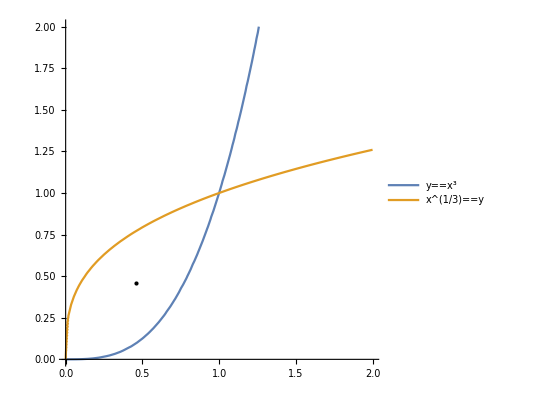

```mathematica
Show[ContourPlot[{y==x^3, x^(1/3)==y},{x,0,2},{y,0,2},Frame->False,Axes->True,PlotLegends->"Expressions"],Graphics[{PointSize[Large],Point[{0.45714,0.45714}]}]]
```

## ejercicios 02

#### Momento de inercia

#### ejercicio 11

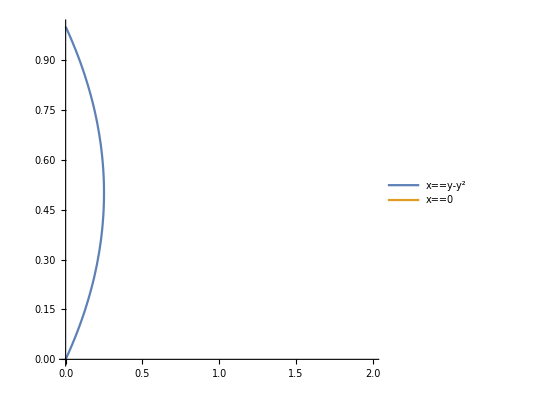

```mathematica
ContourPlot[{x==y-y^2, x==0},{x,0,2},{y,0,1},Frame->False,Axes->True,PlotLegends->"Expressions"]
```

```mathematica
NSolve[{x==y-y^2, x==0},{x,y},Reals]
```

{{x→0,y→0},{x→0,y→1.}}

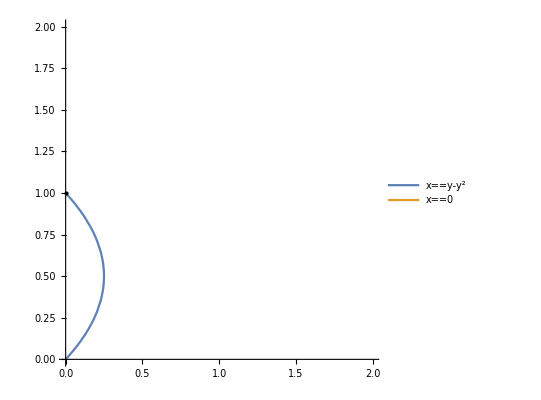

```mathematica
Show[ContourPlot[{x==y-y^2, x==0},{x,0,2},{y,0,2},Frame->False,Axes->True,PlotLegends->"Expressions"],Graphics[{PointSize[Large],Point[{0,1}]}]]
```

```mathematica
∫_0^1 ∫_0^(y-y^2) x^2(2x)ⅆxⅆy
```

1/1260

#### ejercicio 12

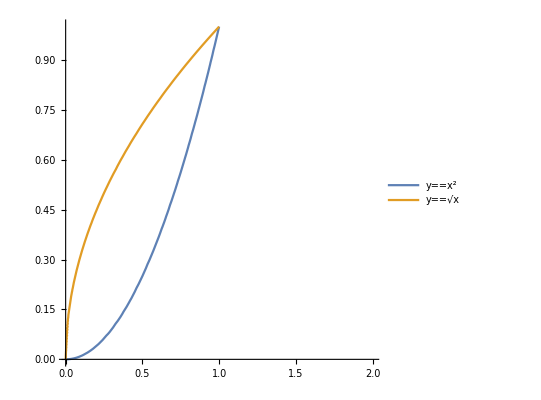

```mathematica
ContourPlot[{y==x^2, y==√x},{x,0,2},{y,0,1},Frame->False,Axes->True,PlotLegends->"Expressions"]
```

```mathematica
NSolve[{y==x^2, y==√x},{x,y},Reals]
```

{{x→1.,y→1.},{x→0.,y→0.}}

```mathematica
∫_0^1 ∫_(x^2)^(√x) x^2 ⅆyⅆx
```

3/35

```mathematica
∫_0^1 ∫_(x^2)^(√x) x^2(x^2)ⅆyⅆx
```

3/77

#### ejercicio 14

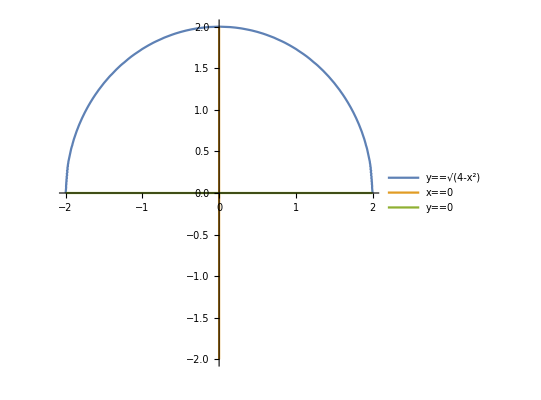

```mathematica
ContourPlot[{y==√(4-x^2), x==0,y==0},{x,-2,2},{y,-2,2},Frame->False,Axes->True,PlotLegends->"Expressions"]
```

```mathematica
NSolve[{y==√(4-x^2), x==0, y==0},{x,y},Reals]
```

{}

## Area superficial

```mathematica
RegionPlot3D[x^2+y^2+z^2<2&&z^2>x^2+y^2,{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->55,
Boxed-> False,AxesOrigin->{0,0,0},PlotRange->All]
```

-Graphics3D-

```mathematica
f=√(2-x^2-y^2);
```

```mathematica
Simplify[1+(D[f,x])^2+(D[f,y])^2]
```

-2/(-2+x^2+y^2)

```mathematica
2N[∫_0^(2π) ∫_0^1 √(2/(2-r^2))rⅆrⅆθ]
```

7.36121

#### ejercicio 7 segundo pdf

```mathematica
RegionPlot3D[x^2+y^2+z^2<25&&4 x^2+y^2<25,{x,0,5 },{y,0,5},{z,0,5},PlotPoints->55,
Boxed-> False,AxesOrigin->{0,0,0},PlotRange->All]
```

-Graphics3D-

```mathematica
f=√(25-x^2-y^2);(*de radio 25*)
```

```mathematica
Simplify[√(1+(D[f,x])^2+(D[f,y])^2)](*calcular las derivadas*)
```

5 √(-1/(-25+x^2+y^2))

```mathematica
5N[∫_0^(5/2) ∫_0^(√(25-4 x^2)) √(1/(25-x^2-y^2))ⅆyⅆx]
```

13.09

#### ejercicio 08

```mathematica
RegionPlot3D[x^2-y^2>z&&4 x^2+y^2<4,{x,0,2 },{y,0,2},{z,0,2},PlotPoints->55,
Boxed-> False,AxesOrigin->{0,0,0},PlotRange->All]
```

-Graphics3D-

```mathematica
f=x^2-y^2;
```

```mathematica
Simplify[√(1+(D[f,x])^2+(D[f,y])^2)]
```

√(1+4 x^2+4 y^2)

```mathematica
N[∫_0^2 ∫_0^(√(4-x^2)) √(1+4 x^2+4 y^2)ⅆyⅆx] (*el limite de y es por despeje de x^2+y^2=4*)
```

9.04423

## Solución de ecuaciones

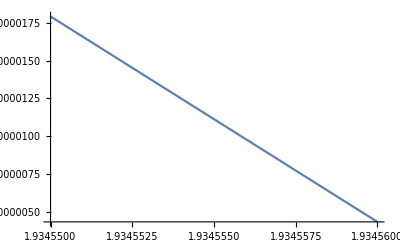

```mathematica
Plot[Sin[x]-x+1,{x,1.93455,1.93456}]
```

#### Bisección

```mathematica
Clear[x]
```

```mathematica
(*introducción al método de bisección*)
f= Sin[X]-x+1;a=1;b=3; c= (a+b)/2;
```

```mathematica
(*entradas del If*)
If[(f/. X-> c)(f/. X->b)<0,a=c,b=c]
```

2

```mathematica
{a,b}
```

{1,2}

```mathematica
a=1.;b=3;
```

```mathematica
Table[c=(a+b)/2;If[(f/.X->c)(f/.X->b)<0,a=c,b=c],{15}]
```

{2.,1.5,1.75,1.875,1.9375,1.90625,1.92188,1.92969,1.93359,1.93555,1.93457,1.93408,1.93433,1.93445,1.93451}